```mathematica
FactorInteger[123278897]
```

{{7,1},{19,1},{821,1},{1129,1}}

```mathematica
Degree
```

°

```mathematica
Series[x^2,{x,1,4}]
```

1+2 (x-1)+(x-1)^2+O[x-1]^5

```mathematica
Dt[x^n,x]
```

x^n (n/x+Dt[n,x] Log[x])

```mathematica
LogicalExpand[(p||q)&&!(r||s)]
```

(p&&!r&&!s)||(q&&!r&&!s)

```mathematica
Reduce[a x-b==0,x]
```

(b==0&&a==0)||(a≠0&&x==b/a)

```mathematica
Reduce[Sin[x]==a,x]
```

C[1]∈Integers&&(x==π-ArcSin[a]+2 π C[1]||x==ArcSin[a]+2 π C[1])

```mathematica
Solve[Sin[x]==a,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→ArcSin[a]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→ArcSin[a]}}

```mathematica
Reduce[x^2+y^2==1,y,Integers]
```

(x==-1&&y==0)||(x==0&&y==-1)||(x==0&&y==1)||(x==1&&y==0)

```mathematica
Reduce[x+y<1&&y>x>0,{x,y}]
```

0<x<1/2&&x<y<1-x

```mathematica
FindInstance[x+y<1&&y^2>x>0,{x,y}]
```

{{x→7/2,y→-3}}

```mathematica
Maximize[{x^2+y,x^2+y^2≤1},{x,y}]
```

{5/4,{x→-(√3)/2,y→1/2}}

```mathematica
DSolve[y'[x]==a y[x]+1,y[x],x]
```

{{y[x]→-1/a+ⅇ^(a x) C[1]}}

```mathematica
DSolve[{y'[x]==a y[x]+1,y[0]==0},y[x],x]
```

{{y[x]→(-1+ⅇ^(a x))/a}}

```mathematica
DSolve[y'[x]==x+y[x],y,x]
```

{{y→Function[{x},-1-x+ⅇ^x C[1]]}}

```mathematica
y''[x]+y[x]/.%
```

{-1-x+2 ⅇ^x C[1]}

```mathematica
Series[1+f[t],{t,0,3}]
```

(1+f[0])+f'[0] t+1/2 f''[0] t^2+1/6 f^(3)[0] t^3+O[t]^4

```mathematica
Normal[%]
```

1+f[0]+t f'[0]+1/2 t^2 f''[0]+1/6 t^3 f^(3)[0]

```mathematica
Limit[Sin[x]/x,x->0]
```

1

```mathematica
LaplaceTransform[t^3 ⅇ^(a t),t,s]
```

6/(a-s)^4

```mathematica
InverseLaplaceTransform[%,s,t]
```

ⅇ^(a t) t^3

```mathematica
FourierTransform[t^4 ⅇ^(-t^2),t,w]
```

(ⅇ^(-w^2/4) (12-12 w^2+w^4))/(16 √2)

```mathematica
InverseFourierTransform[%,w,t]
```

ⅇ^(-t^2) t^4

```mathematica
RSolve[{a[n]==3 a[n-1]+1,a[1]==1},a[n],n]
```

{{a[n]→1/2 (-1+3^n)}}

```mathematica
<<VectorAnalysis`
```

```mathematica
SetCoordinates[Spherical[r,theta,phi]]
```

Spherical[r,theta,phi]

```mathematica
Grad[r^2 Sin[θ]]
```

{2 r Sin[θ],0,0}

```mathematica
?Grad
```

RowBox[{"Grad", "[", StyleBox["f", "TI"], "]"}] gives the gradient, RowBox[{"∇", StyleBox["f", "TI"]}], of the scalar function StyleBox["f", "TI"] in the default coordinate system. 
RowBox[{"Grad", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["coordsys", "TI"]}], "]"}] gives the gradient of StyleBox["f", "TI"] in the coordinate system StyleBox["coordsys", "TI"].

```mathematica
?Div
```

RowBox[{"Div", "[", StyleBox["f", "TI"], "]"}] gives the divergence, RowBox[{"∇", RowBox[{"·", StyleBox["f", "TI"]}]}], of the vector field StyleBox["f", "TI"] in the default coordinate system. 
RowBox[{"Div", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["coordsys", "TI"]}], "]"}] gives the divergence of StyleBox["f", "TI"] in the coordinate system StyleBox["coordsys", "TI"].

```mathematica
?Curl
```

RowBox[{"Curl", "[", StyleBox["f", "TI"], "]"}] gives the curl, RowBox[{"∇", RowBox[{"×", StyleBox["f", "TI"]}]}], of the vector field StyleBox["f", "TI"] in the default coordinate system. 
RowBox[{"Curl", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["coordsys", "TI"]}], "]"}] gives the curl of StyleBox["f", "TI"] in the coordinate system StyleBox["coordsys", "TI"].

```mathematica
?Laplacian
```

RowBox[{"Laplacian", "[", StyleBox["f", "TI"], "]"}] gives the Laplacian, RowBox[{SuperscriptBox["∇", "2"], StyleBox["f", "TI"]}], of the scalar function or vector field StyleBox["f", "TI"] in the default coordinate system. 
RowBox[{"Laplacian", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["coordsys", "TI"]}], "]"}] gives the Laplacian of StyleBox["f", "TI"] in the coordinate system StyleBox["coordsys", "TI"].

```mathematica
NIntegrate[Sin[x y],{x,0,1},{y,0,x}]
```

0.119906

```mathematica
Plot3D[Sin[x y],{x,0,1},{y,0,x}]
```

-Graphics3D-

```mathematica
NDSolve[{y'[x]==y[x],y[0]==1},y,{x,0,2}]
```

{{y→InterpolatingFunction[{{0.,2.}},<>]}}

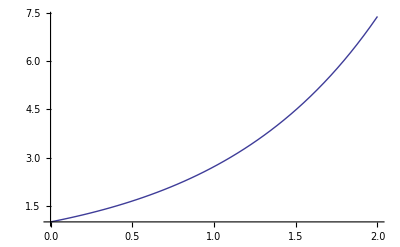

```mathematica
Plot[y[x]/.%,{x,0,2}]
```

```mathematica
NDSolve[{y'[x]==z[x],z'[x]==-y[x],y[0]==0,z[0]==1},{y,z},{x,0,Pi}]
```

{{y→InterpolatingFunction[{{0.,3.14159}},<>],z→InterpolatingFunction[{{0.,3.14159}},<>]}}

```mathematica
z[2]/.%
```

{-0.416147}

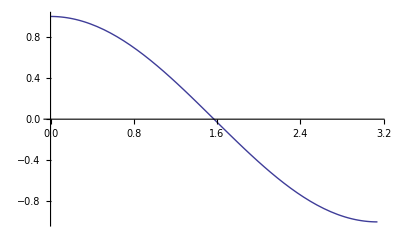

```mathematica
Plot[Evaluate[z[x]/.%36],{x,0,Pi}]
```

```mathematica
??Evaluate
```

RowBox[{"Evaluate", "[", StyleBox["expr", "TI"], "]"}] causes StyleBox["expr", "TI"] to be evaluated even if it appears as the argument of a function whose attributes specify that it should be held unevaluated.

Attributes[Evaluate]={Protected}

```mathematica
Plot[z[x]/.%36,{x,0,Pi}]
```

-Graphics-

```mathematica
NMaximize[x/(1+Exp[x]),x]
```

{0.278465,{x→1.27846}}

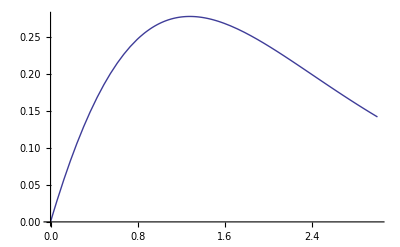

```mathematica
Plot[x/(1+Exp[x]),{x,0,3}]
```

```mathematica
NMinimize[{Cos[x]-Exp[x y],x^2+y^2<1},{x,y}]
```

{-0.919441,{x→0.795976,y→0.605329}}

```mathematica
Plot3D[Cos[x]-Exp[x y],{x,0,1},{y,0,1},RegionFunction->Function[{x,y},x^2+y^2<1]]
```

-Graphics3D-

```mathematica
FindMinimum[x Cos[x],{x,2}]
```

{-3.28837,{x→3.42562}}

```mathematica
FindMinimum[x Cos[x],{x,10}]
```

{-9.47729,{x→9.52933}}

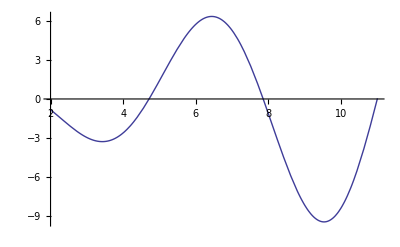

```mathematica
Plot[x Cos[x],{x,2,11}]
```

```mathematica
FindMinimum[Sin[x y],{{x,2},{y,2}}]
```

{-1.,{x→2.1708,y→2.1708}}

```mathematica
Plot3D[Sin[x y],{x,2,3},{y,2,3}]
```

-Graphics3D-

```mathematica
data=Table[Exp[x/5.],{x,7}]
```

{1.2214,1.49182,1.82212,2.22554,2.71828,3.32012,4.0552}

```mathematica
Fit[data,{1,x,x^2},x]
```

1.09428+0.0986337 x+0.0459482 x^2

```mathematica
Fit[data,{1,x,x^3,x^5},x]
```

0.96806+0.246829 x+0.00428281 x^3-6.57948×10^-6 x^5

```mathematica
data=Table[{x,Exp[Sin[x]]},{x,0.,1.,0.2}]
```

{{0.,1.},{0.2,1.21978},{0.4,1.47612},{0.6,1.75882},{0.8,2.04901},{1.,2.31978}}

```mathematica
Fit[%,{1,Sin[x],Sin[2x]},x]
```

0.989559+2.04199 Sin[x]-0.418176 Sin[2 x]

```mathematica
FindFit[data,a+b x+c x^2,{a,b,c},x]
```

{a→0.991251,b→1.16421,c→0.174256}

```mathematica
FindFit[data,a+b^(c+d x),{a,b,c,d},x]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{a→-3.65199,b→1.65715,c→3.0394,d→0.501802}

```mathematica
data={1,1,1,1,-1,-1,-1,-1}
```

{1,1,1,1,-1,-1,-1,-1}

```mathematica
Fourier[data]
```

{0.+0. ⅈ,0.707107+1.70711 ⅈ,0.+0. ⅈ,0.707107+0.292893 ⅈ,0.+0. ⅈ,0.707107-0.292893 ⅈ,0.+0. ⅈ,0.707107-1.70711 ⅈ}

```mathematica
data={4.3,7.2,8.4,5.8,9.2,3.9}
```

{4.3,7.2,8.4,5.8,9.2,3.9}

```mathematica
Mean[data]
```

6.46667

```mathematica
Variance[data]
```

4.69467

```mathematica
Median[data]
```

6.5

```mathematica
StandardDeviation[data]
```

2.16672

```mathematica
Quantile[data,1/2]
```

5.8

```mathematica
Total[data]
```

38.8

```mathematica
1+f[x]+f[y]/.f[x]->p
```

1+p+f[y]

```mathematica
1+f[x]+f[y]/.f[t_]->t^2
```

1+x^2+y^2

```mathematica
1+x^2+x^4/.x^p_->f[p]
```

1+f[2]+f[4]

```mathematica
{{a,b},{c,d}}//ColumnForm
```

{a,b}
{c,d}

```mathematica
{{a,b},{c,d}}//TableForm
```

a | b
c | d

```mathematica
{{a,b},{c,d}}//MatrixForm
```

(a | b
c | d)

```mathematica
m={{a,b},{c,d}}
```

{{a,b},{c,d}}

```mathematica
Det[m]
```

-b c+a d

```mathematica
Transpose[m]
```

{{a,c},{b,d}}

```mathematica
Inverse[m]
```

{{d/(-b c+a d),-b/(-b c+a d)},{-c/(-b c+a d),a/(-b c+a d)}}

```mathematica
Eigenvalues[m]
```

{1/2 (a+d-√(a^2+4 b c-2 a d+d^2)),1/2 (a+d+√(a^2+4 b c-2 a d+d^2))}

```mathematica
Eigenvectors[m]
```

{{-(-a+d+√(a^2+4 b c-2 a d+d^2))/(2 c),1},{-(-a+d-√(a^2+4 b c-2 a d+d^2))/(2 c),1}}

```mathematica
Tr[m]
```

a+d

```mathematica
MatrixPower[m,3]
```

{{a (a^2+b c)+b (a c+c d),a (a b+b d)+b (b c+d^2)},{c (a^2+b c)+d (a c+c d),c (a b+b d)+d (b c+d^2)}}

```mathematica
m=IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
FreeQ[m,0]
```

False

```mathematica
Position[m,0]
```

{{1,2},{1,3},{2,1},{2,3},{3,1},{3,2}}

```mathematica
m={{a,b},{c,d}}
```

{{a,b},{c,d}}

```mathematica
m[[All,1]]={x,y};m
```

{{x,b},{y,d}}

```mathematica
m[[All,1]]=0;m
```

{{0,b},{0,d}}

```mathematica
Tuples[{a,b},2]
```

{{a,a},{a,b},{b,a},{b,b}}

```mathematica
Tuples[{a,b,c},2]
```

{{a,a},{a,b},{a,c},{b,a},{b,b},{b,c},{c,a},{c,b},{c,c}}

```mathematica
Tuples[{{a,b},{1,2,3}}]
```

{{a,1},{a,2},{a,3},{b,1},{b,2},{b,3}}

```mathematica
t={17,21,14,9,18}
```

{17,21,14,9,18}

```mathematica
Min[t]
```

9

```mathematica
Ordering[t,3]
```

{4,3,1}

```mathematica
t[[%]]
```

{9,14,17}

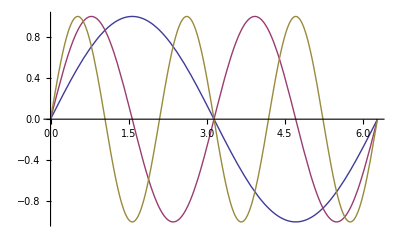

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi}]
```

```mathematica
Table[BesselJ[n,x],{n,4}]
```

{BesselJ[1,x],BesselJ[2,x],BesselJ[3,x],BesselJ[4,x]}

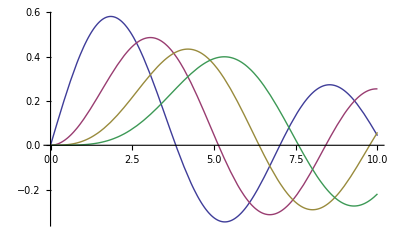

```mathematica
Plot[%,{x,0,10}]
```

```mathematica
??InterpolatingFunction
```

RowBox[{"InterpolatingFunction", "[", RowBox[{StyleBox["domain", "TI"], ",", StyleBox["table", "TI"]}], "]"}] represents an approximate function whose values are found by interpolation.

Attributes[InterpolatingFunction]={Protected,ReadProtected}

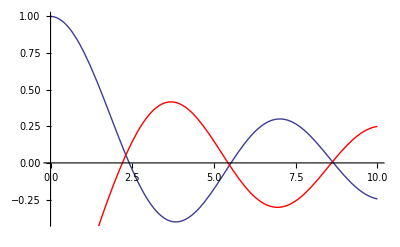

```mathematica
gj0=Plot[BesselJ[0,x],{x,0,10}];
gy1=Plot[BesselY[1,x],{x,1,10},PlotStyle->Red];
gjy=Show[gj0,gy1]
```

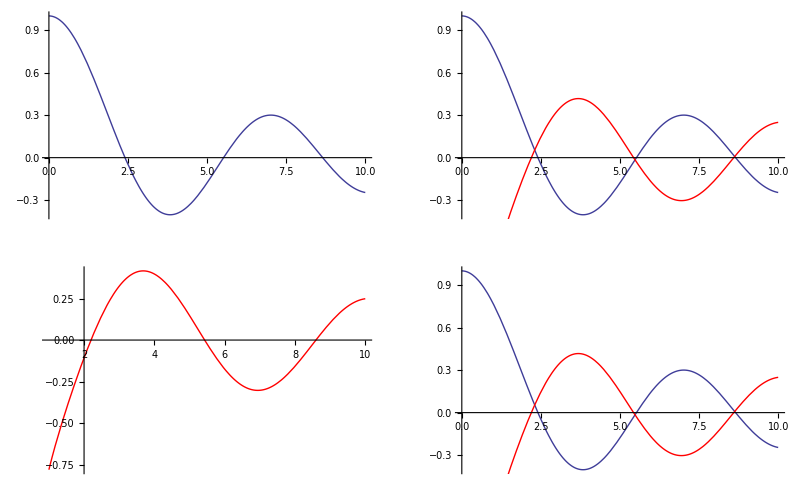

```mathematica
Show[GraphicsArray[{{gj0,gjy},{gy1,gjy}}]]
```

```mathematica
Options[Plot,PlotRange]
```

{PlotRange→{Full,Automatic}}

```mathematica
SetOptions[Plot,PlotRange->All];
```

```mathematica
Options[Plot,PlotRange]
```

{PlotRange→All}

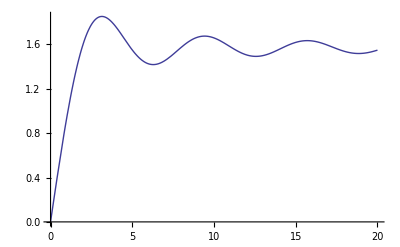

```mathematica
g=Plot[SinIntegral[x],{x,0,20}]
```

```mathematica
SinIntegral'[x]
```

Sin[x]/x

```mathematica
Options[g,PlotRange]
```

{PlotRange→{All,All}}

```mathematica
AbsoluteOptions[g,PlotRange]
```

{PlotRange→{{4.08163×10^-7,20.},{4.08163×10^-7,1.85194}}}

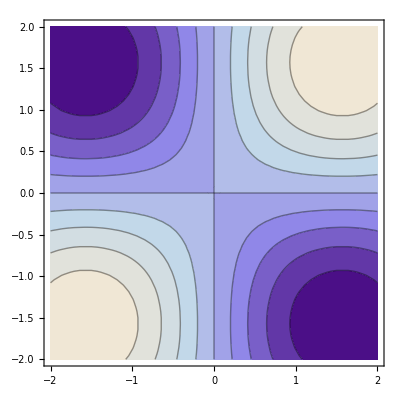

```mathematica
ContourPlot[Sin[x] Sin[y],{x,-2,2},{y,-2,2}]
```

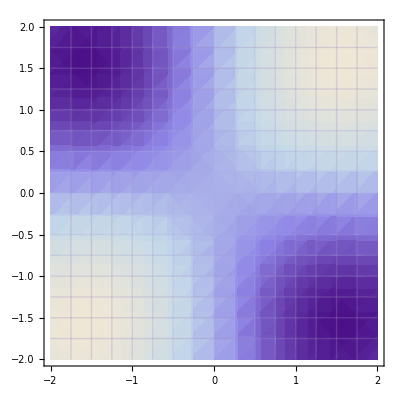

```mathematica
DensityPlot[Sin[x] Sin[y],{x,-2,2},{y,-2,2},Mesh->True]
```

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3}]
```

-Graphics3D-

```mathematica
Plot3D[BesselJ[nu,3x],{nu,0,3},{x,0,3}]
```

-Graphics3D-

```mathematica
t=Table[i^2,{i,10}]
```

{1,4,9,16,25,36,49,64,81,100}

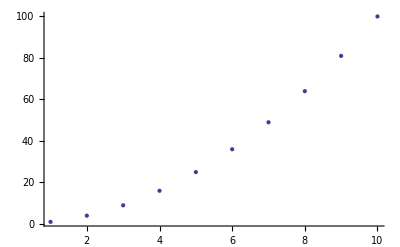

```mathematica
ListPlot[t]
```

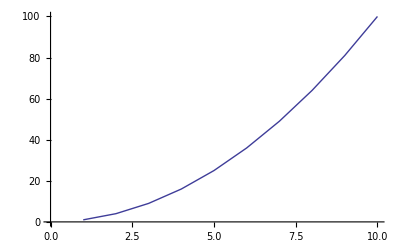

```mathematica
ListPlot[t,Joined->True]
```

```mathematica
Table[{i^2,4 i^2+i^3},{i,10}]
```

{{1,5},{4,24},{9,63},{16,128},{25,225},{36,360},{49,539},{64,768},{81,1053},{100,1400}}

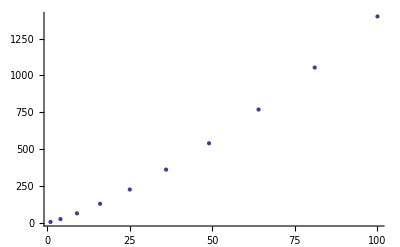

```mathematica
ListPlot[%]
```

```mathematica
t3=Table[Mod[x,y],{y,20},{x,30}];
```

```mathematica
ListPlot3D[t3]
```

-Graphics3D-

```mathematica
Show[%,ViewPoint->{1.5,-0.5,0}]
```

-Graphics3D-

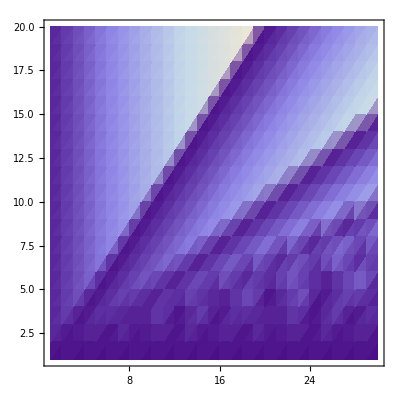

```mathematica
ListDensityPlot[t3]
```

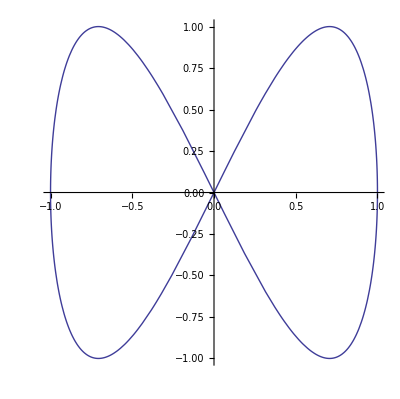

```mathematica
ParametricPlot[{Sin[t],Sin[2t]},{t,0,2Pi}]
```

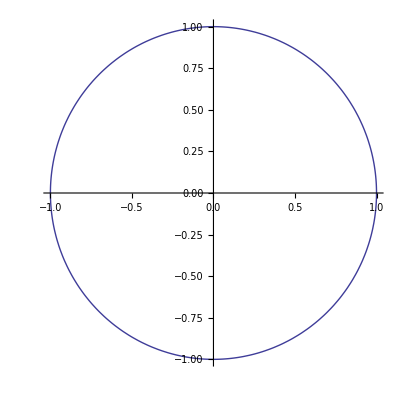

```mathematica
ParametricPlot[{Sin[t],Cos[t]},{t,0,2Pi}]
```

```mathematica
ParametricPlot3D[{Sin[t],Cos[t],t/3},{t,0,15}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{t,u,Sin[t u]},{t,0,3},{u,0,3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{t,u^2,Sin[t u]},{t,0,3},{u,0,3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u Sin[t],u Cos[t],t/3},{t,0,15},{u,-1,1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[t],Cos[t],u},{t,0,2Pi},{u,0,4}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t] (3+Cos[u]),Sin[t] (3+Cos[u]),Sin[u]},{t,0,2Pi},{u,0,2Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t] Cos[u],Sin[t] Cos[u],Sin[u]},{t,0,2Pi},{u,-Pi/2,Pi/2}]
```

-Graphics3D-

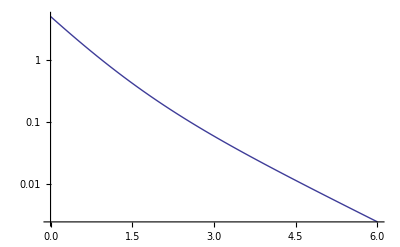

```mathematica
LogPlot[Exp[-x]+4 Exp[-2x],{x,0,6}]
```

```mathematica
p=Table[Prime[n],{n,10}]
```

{2,3,5,7,11,13,17,19,23,29}

```mathematica
<<Graphics`Graphics`
```

General::obspkg: "Graphics`Graphics`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

TextListPlot::shdw: Symbol "TextListPlot" appears in multiple contexts {"Graphics`Graphics`", "Global`"}; definitions in context "Graphics`Graphics`" may shadow or be shadowed by other definitions.

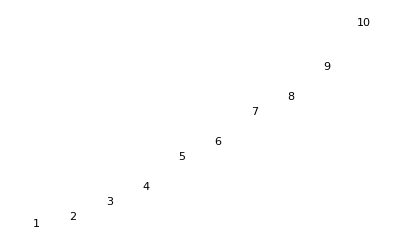

```mathematica
TextListPlot[p]
```

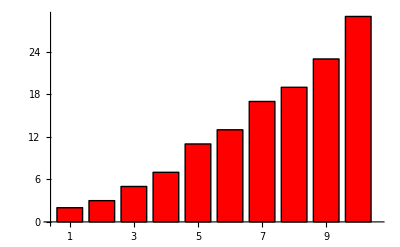

```mathematica
BarChart[p]
```

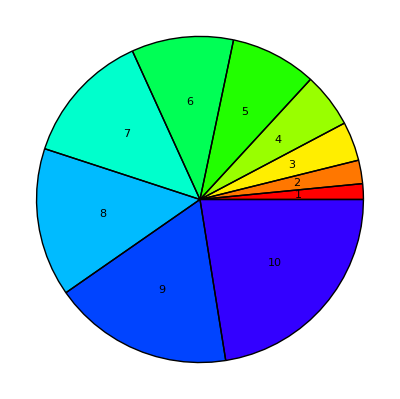

```mathematica
PieChart[p]
```

```mathematica
<<Graphics`Animation`
```

General::obspkg: "Graphics`Animation`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

Set::wrsym: Symbol ShowAnimation is Protected.

```mathematica
Table[Plot3D[BesselJ[0,Sqrt[x^2+y^2]+t],{x,-10,10},{y,-10,10},Axes->False,PlotRange->{-0.5,1.0},DisplayFunction->Identity],{t,0,8}];
```

```mathematica
ShowAnimation[%]
```

```mathematica
Animate[Plot3D[BesselJ[0,Sqrt[x^2+y^2]+t],{x,-10,10},{y,-10,10},Axes->False,PlotRange->{-0.5,1.0},DisplayFunction->Identity],{t,0,8,0.5}]
```

```mathematica
Play[Sin[2Pi 440 t],{t,0,1}]
```

-Graphics-

```mathematica
Play[Sin[700 t+25 t Sin[350 t]],{t,0,4}]
```

-Graphics-

```mathematica
x_⊕y_:=Mod[x+y,2]
```

```mathematica
{17⊕5,8⊕3}
```

{0,1}

```mathematica
Sqrt[x]+1/(2+Sqrt[y])//OutputForm
```

1
Sqrt[x] + -----------
          2 + Sqrt[y]

```mathematica
∫1/(x^3+1)ⅆx
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
∫1/(x^3+1)ⅆx//TraditionalForm
```

(tan^-1((2 x-1)/(√3)))/(√3)+1/3 log(x+1)-1/6 log(x^2-x+1)

```mathematica
{Abs[x],ArcTan[x],BesselJ[0,x],Binomial[i,j]}//TraditionalForm
```

{|x|,tan^-1(x),J_0(x),(i
j)}

```mathematica
{Ci[1+x],CosIntegral[1+x],Ci(1+x)}//StandardForm
```

{Ci[1+x],CosIntegral[1+x],Ci (1+x)}

```mathematica
{Ci[1+x],CosIntegral[1+x],Ci(1+x)}//TraditionalForm
```

{Ci(x+1),Ci(x+1),Ci (x+1)}

```mathematica
TeXForm[%]
```

\frac{(x+y)^2}{\sqrt{x y}}

```mathematica
ToExpression["\\sqrt{x y}",TeXForm]
```

√xy

```mathematica
MathMLForm[x^2/z]
```

<math>
 <mfrac>
  <msup>
   <mi>x</mi>
   <mn>2</mn>
  </msup>
  <mi>z</mi>
 </mfrac>
</math>

```mathematica
ToExpression["<math> 
<mfrac> 
  <msup> 
    <mi>x</mi> 
    <mn>2</mn> 
  </msup> 
  <mi>z</mi> 
</mfrac> 
</math> 
",MathMLForm]
```

x^2/z

```mathematica
Expand[(1+x+y)^2]
```

1+2 x+x^2+2 y+2 x y+y^2

```mathematica
FortranForm[%]
```

1 + 2*x + x**2 + 2*y + 2*x*y + y**2

```mathematica
CForm[%]
```

1 + 2*x + Power(x,2) + 2*y + 2*x*y + Power(y,2)

```mathematica
Compile[x,%]
```

CompiledFunction[{x},%,-CompiledCode-]